```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
PartLoopByGreedyFromSort[SortList_]:=((* 入力として枝のコストの順位を与えられたときのGreedyを使った部分巡回路の構築 *)
EdgeSolution={};
EdgeProcess={Ruleg[[SortList[[1]]]]};
For[j=2,
EdgeSolution=={},
j++,
AppendEdgeProcess=Append[EdgeProcess,Ruleg[[SortList[[j]]]]];
If[Max[VertexDegree[AppendEdgeProcess]]≤2,
If[AcyclicGraphQ[UndirectedGraph[AppendEdgeProcess]],
EdgeProcess=AppendEdgeProcess,
EdgeSolution=AppendEdgeProcess
]
]
];
EdgeSolution=EdgeRules[FindCycle[UndirectedGraph[EdgeSolution]][[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
DelEle[list_,element_]:=Delete[list,FirstPosition[list,element]](* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=Delete[list,Table[FirstPosition[list,i],{i,elementlist}]](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair ２つの枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアーとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
PartLoopByNewUndirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮しない、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
UndirectedGraph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
PartLoopByNewDirectedGreedyFromSort[SortList_]:=((* 枝の向きを考慮する、入力として枝のコストの順位を与えられたときの新しいGreedyを使った部分巡回路の構築(コストは優先順位が高い順にでソートされる) *)
EdgeSolution={};
For[i=3,Length[EdgeSolution]==0,i++,
EdgeSolution=FindCycle[
Graph[EdgeList[Gout][[SortList[[Range[i]]]]]],
Infinity,All];
];
EdgeSolution=EdgeRules[EdgeSolution[[1]]];
VertexSortFromLoopEdgeList[EdgeSolution]
)
```

```mathematica
RestEdgeSort[Edge_,Cost_]:=
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]][[
Ordering[Cost[[
EdgeNumList[DelEdgeVertexList[Ruleg,VertexList[Edge]]
]]]]
]](* 残りの枝でのソート(与えられた枝をRulegから引いたエッジリストの中でのソート) *)
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)
```

### 自動表示

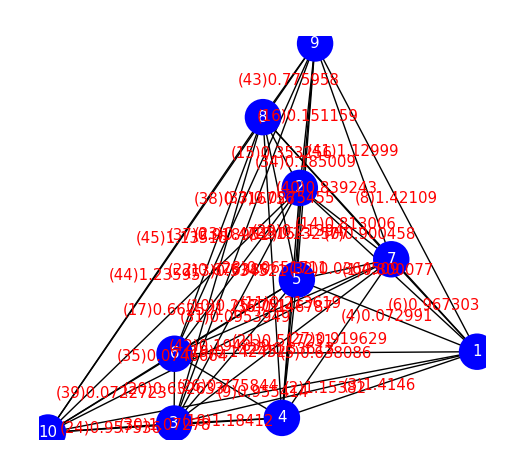

{16.1176,{2,7,5,4,6,8,2}}

{26.8798,{1,7,9,8,2,5,6,10,3,4,1}}

2

```mathematica
TourCost=0;
MathematicaSolution={0,{}};
For[RpeatCount=1,TourCost== MathematicaSolution[[1]],RpeatCount++,
Pin=Table[{RandomReal[10],RandomReal[10]},{i,10}];(*Point input*)
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];(*Ggraph input*)
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
SortCurr=Reverse[Ordering[Abs[Curr]]];
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
PDCurrCost=Abs[PD/Curr ];
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *);
PartLoopByNewDirectedGreedyFromSort[PDCurrCostSort];
OutLoop1={EdgeSolution};
OutLoop1=ContinuousInsertVertexLoop[OutLoop1[[1]]];
VertexSolution=VertexSortFromLoopEdgeList[OutLoop1[[-1]]];
TourCost=Total[EdgeDList[OutLoop1[[-1]]]];
MathematicaSolution=FindShortestTour[Pin];
]
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
{TourCost,VertexSolution}
MathematicaSolution
RpeatCount
```

```mathematica
OutLoop1
```

{{4→7,7→8,8→6,6→4},{4→7,8→6,6→4,7→2,2→8},{8→6,6→4,7→2,2→8,4→5,5→7}}

{26.8798,{1,7,9,8,2,5,6,10,3,4,1}}

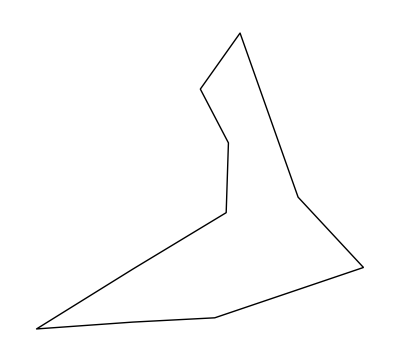

```mathematica
MathematicaSolution
Graphics[Line[Pin[[Last[%]]]]]
```

```mathematica
PDCurrCostSort
```

{18,20,43,6,24,14,3,26,41,27,30,15,40,8,2,37,1,44,7,13,25,45,9,22,5,38,21,17,12,23,16,10,11,34,19,31,36,29,42,39,32,4,35,28,33}

```mathematica
Total[EdgeDList[{4->9,9->6,6->10}]]
```

7.79288

```mathematica
Total[EdgeDList[{4->6,6->9,9->10}]]
```

9.47263

```mathematica
TriTourDiff[9->10,6]
```

0.00373973

```mathematica
TriTourDiff[4->9,6]
```

1.68349

```mathematica
Pin
```

{{9.74997,2.54783},{6.2203,5.81193},{3.71653,1.11667},{5.86331,1.22919},{6.16159,3.98391},{3.72481,2.50755},{8.04133,4.38989},{5.48575,7.2216},{6.52432,8.68946},{1.20419,0.93775}}